```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
FEq =λ*F-σ*(1-R)*F +ρ* R * H;
HEq =σ*(1-R)*F - ρ* R*H - μ*H;

FIEq =λ*FI-σ2*(1-R)*FI +ρ2* R * HI;
HIEq =σ2*(1-R)*FI- ρ2* R*HI - μ*HI;

REq=α*R*(1-R) -(ρ*H + β*F +ρ2*HI + β2*FI )*R ;

Solutions=FullSimplify[Solve[{FEq==0,HEq==0,FIEq==0,HIEq==0,REq==0},{F,H,FI,HI,R}]];
SolutionsF = Diagonal[{F,FI}/.Solutions[[3;;4]]]
```

{(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2))}

```mathematica
StarvationThreshold=Quiet[Table[
chis=chi/.Solve[(1-0.0202 m^0.18999999999999995)/(1+chi)==1/.m->10^i,chi][[1]];
{10^i,chis},
{i,0,8,0.001}]];
```

```mathematica
Invade = ParallelTable[
M = 10^MassExp;
chimin=Quiet[chi/.Solve[(1-0.0202 m^0.18999999999999995)/(1+chi)==1/.m->10^MassExp,chi][[1]]];
tic = (MassExp-0)/0.001 +1;
FSol = SolutionsF[[1]]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderMaintenance};
FISol = SolutionsF[[2]]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderMaintenance};
ChiRange = Table[x,{x,chimin+0.001,1,0.001}];
Test = Table[(Re[FISol]>Re[FSol]),{chi,ChiRange}];
ChiHigher=ChiRange[[Flatten[Position[Test,True],1]]];
{M,ChiHigher},
{MassExp,0,8,0.001}];
```

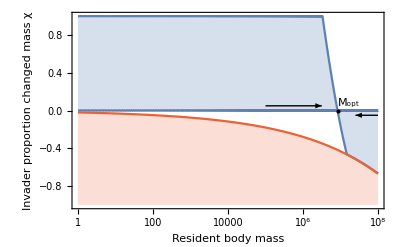

```mathematica
MinMass =Table[{Invade[[i]][[1]],Min[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
MaxMass =Table[{Invade[[i]][[1]],Max[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
InvasionPlot=Show[{
ListLogLinearPlot[{MinMass,MaxMass},Filling->{1->{2}},FillingStyle->Directive[ColorData[97,1],Opacity[0.25]],Joined->True,PlotRange->{{1,10^8},{-1,1}},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{"Resident body mass","Invader proportion changed mass χ"}],
ListLogLinearPlot[StarvationThreshold,Joined->True,PlotRange->{-1,0},PlotStyle->ColorData[97,4],Filling->Bottom],
Graphics[{PointSize[Large],Point[{Log@(8.43*10^6),0}]}],
Graphics[Text["M_opt",{Log@(8.43*10^6.3),0.08}]],
Graphics[{Black,Thick,Arrow[{{Log@(10^5),0.05},{Log@(10^6.5),0.05}}]}],
Graphics[{Black,Thick,Arrow[{{Log@(10^8),-0.05},{Log@(10^7.4),-0.05}}]}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Invasion.pdf",InvasionPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Invasion.pdf

```mathematica
mm=Table[10^x,{x,0,8,0.001}];
```

```mathematica
mm[[6927]]
```

8.43335×10^6